```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/plotting_routines

## solution data

```mathematica
M13 = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/results/unsteady_lid_driven_cavity_odd/result_M13.txt","Table"];
```

```mathematica
DVMSol = Import["/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Traditional/generic_2D/sbp_sat/DVM/unsteady_lid_driven_cavity/result_n100_DVM_20.txt","Table"];
```

```mathematica
GetQ[data_]:=Module[{qx,qy},

qx = Table[{{data⟦1,ii⟧,data⟦2,ii⟧},data⟦-2,ii⟧},{ii,1,Length[data⟦1⟧]}];
qy = Table[{{data⟦1,ii⟧,data⟦2,ii⟧},data⟦-1,ii⟧},{ii,1,Length[data⟦1⟧]}];

qx = Interpolation[qx];
qy = Interpolation[qy];

{qx,qy}
]
```

```mathematica
GetTheta[data_]:=Module[{theta},

theta = Table[{{data⟦1,ii⟧,data⟦2,ii⟧},data⟦6,ii⟧},{ii,1,Length[data⟦1⟧]}];

theta = Interpolation[theta];

theta
]
```

## Results

```mathematica
ThetaM13 = GetTheta[M13];
HeatFluxM13 = GetQ[M13];
HeatFluxDVM = GetQ[DVMSol];
```

```mathematica
contour=ContourPlot[ThetaM13[x,y],{x,0,1},{y,0,1},ColorFunction->"TemperatureMap",ContourLabels->False,ContourLines->False,Frame->True,FrameTicksStyle->Directive[Black,20],ImageSize->600,BaseStyle->{FontSize->15},FrameLabel->{{Style["x_2",FontSize->20],None},{Style["x_1",FontSize->20],None}},RotateLabel->False,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->16}],PlotLabel->Style["θ̃(x_1,x_2,t=1)",FontSize->20,FontColor->Black],PlotRange->Full];

streamlines=StreamPlot[{HeatFluxM13⟦1⟧[x,y],HeatFluxM13⟦2⟧[x,y]},{x,0,1},{y,0,1},StreamPoints->{Automatic,0.05},ImageSize->Large,StreamStyle->{Black},Frame->True,FrameTicksStyle->16];

streamlinesDVM=StreamPlot[{HeatFluxDVM⟦1⟧[x,y],HeatFluxDVM⟦2⟧[x,y]},{x,0,1},{y,0,1},StreamPoints->{Automatic,0.05},ImageSize->Large,StreamStyle->{Green,Dashed},Frame->True,FrameTicksStyle->16];
```

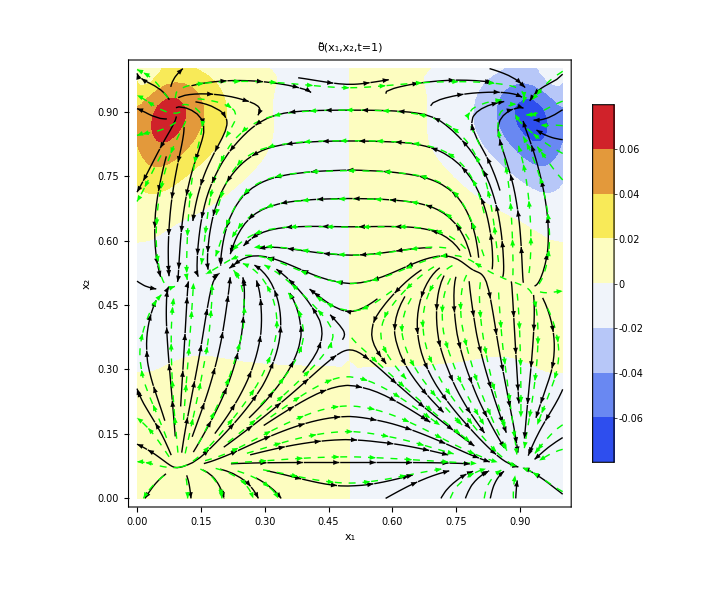

```mathematica
finalPlot=Show[{contour,streamlines,streamlinesDVM}]
```

```mathematica
filename = "/Users/neerajsarna/Dropbox/my_papers/Publications/Comparitive_BC/results/unsteady_lid_driven_cavity/theta.eps";
Export[filename,finalPlot]
```

/Users/neerajsarna/Dropbox/my_papers/Publications/Comparitive_BC/results/unsteady_lid_driven_cavity/theta.eps